```mathematica
p=0;
s=0.05;
x0=0.5;
b=3;
c=1;
N0=4;
k=100;
```

```mathematica
original=NDSolve[{D[x[t],t]==-s*(1+p*x[t])*x[t]*(1-x[t]),D[n[t],t]==n[t]*((1+p*x[t])-n[t]/k),n[0]==N0,x[0]==x0},{x,n},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],n→InterpolatingFunction[{{0.,10.}},<>]}}

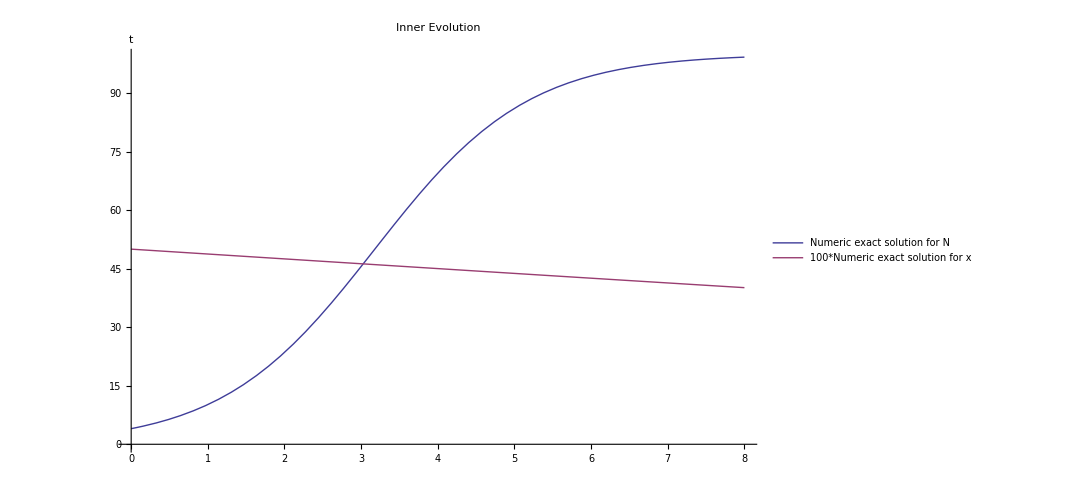

```mathematica
Plot[{Evaluate[n[t]/.original],100*Evaluate[x[t]/.original]},{t,0,8},PlotLegends->Placed[{"Numeric exact solution for N","100*Numeric exact solution for x"},{0.65,0.8}],AxesLabel->{"t"},PlotLabel->"Inner Evolution",ImageSize->800]
```

```mathematica
n[4.56435]/.original
```

{80.}

```mathematica
x[4.56435]/.original
```

{0.443192}

```mathematica
original0=NDSolve[{D[x[t],t]==-s*(1+p*x[t])*x[t]*(1-x[t]),D[n[t],t]==n[t]*((1+p*x[t])-n[t]/k),n[0]==N0,x[0]==0},{x,n},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],n→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
n[4.56435]/.original0
```

{80.}

```mathematica
x[4.56435]/.original0
```

{0.}

```mathematica
original025=NDSolve[{D[x[t],t]==-s*(1+p*x[t])*x[t]*(1-x[t]),D[n[t],t]==n[t]*((1+p*x[t])-n[t]/k),n[0]==N0,x[0]==0.25},{x,n},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],n→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
n[4.56435]/.original025
```

{80.}

```mathematica
x[4.56435]/.original025
```

{0.209684}

```mathematica
original075=NDSolve[{D[x[t],t]==-s*(1+p*x[t])*x[t]*(1-x[t]),D[n[t],t]==n[t]*((1+p*x[t])-n[t]/k),n[0]==N0,x[0]==0.75},{x,n},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],n→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
n[4.56435]/.original075
```

{80.}

```mathematica
x[4.56435]/.original075
```

{0.704828}

```mathematica
original1=NDSolve[{D[x[t],t]==-s*(1+p*x[t])*x[t]*(1-x[t]),D[n[t],t]==n[t]*((1+p*x[t])-n[t]/k),n[0]==N0,x[0]==1.},{x,n},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],n→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
n[4.56435]/.original1
```

{80.}

```mathematica
x[4.56435]/.original1
```

{1.}

```mathematica
somma=0; (*Here I do the one for x[0]=0.75 *)
For[i=0;pr=0.209684,i≤4,i++,t=Binomial[N0,i]*(pr^i)*((1-pr)^(N0-i));somma=somma+t;Print[N[t]]]
```

0.390124

0.414026

0.164772

0.0291445

0.00193313

```mathematica
somma
```

1.